```mathematica
(* Define *)
(*β = (1/2)rho0 cd A/(mdry)*)
eqns={h'[t] == v[t], v'[t] == -β v[t]^2-g,
h[0] == h0, v[0] == v0, v[tf] == 0}
```

{h'[t]==v[t],v'[t]==-g-β v[t]^2,h[0]==h0,v[0]==v0,v[tf]==0}

```mathematica
sols=DSolve[eqns,{h[t],v[t]},{t}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -g+g Cos[√g √β C[1]]^2+v0^2 β Cos[√g √β C[1]]^2 == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -g/(√β)+(g Cos[√g √β C[1]]^2)/(√β)+v0^2 √β Cos[√g √β C[1]]^2 == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-(√g Tan[√g t √β-√g tf √β])/(√β),h[t]→(h0 β-Log[-(√g)/(√(g+v0^2 β))]+Log[Cos[√g (t-tf) √β]])/β},{v[t]→-(√g Tan[√g t √β-√g tf √β])/(√β),h[t]→(h0 β-Log[(√g)/(√(g+v0^2 β))]+Log[Cos[√g (t-tf) √β]])/β}}

```mathematica
hsol1=h[t]/.sols[[1]]
hsol2 = h[t]/.sols[[2]]
```

(h0 β-Log[-(√g)/(√(g+v0^2 β))]+Log[Cos[√g (t-tf) √β]])/β

(h0 β-Log[(√g)/(√(g+v0^2 β))]+Log[Cos[√g (t-tf) √β]])/β

```mathematica
(*Its clear from the negative in hsol1's first log that it is infeasible*)
```

```mathematica
vsol1=v[t]/.sols[[1]]
vsol2 = v[t]/.sols[[2]]
```

-(√g Tan[√g t √β-√g tf √β])/(√β)

-(√g Tan[√g t √β-√g tf √β])/(√β)

```mathematica
(*And vsol1 and vsol2 are identical*)
```

```mathematica
Assuming[h0>0 && g>0 && β>0&&v0>0,ExpandAll[Simplify[hsol1]]]
Assuming[h0>0 && g>0 && β>0&&v0>0,ExpandAll[Simplify[vsol1]]]
```

h0-Log[-√(g/(g+v0^2 β))]/β+Log[Cos[t √(g β)-tf √(g β)]]/β

-√(g/β) Tan[t √(g β)-tf √(g β)]

```mathematica
hsol=Assuming[h0>0 && g>0 && β>0&&v0>0,ExpandAll[Simplify[hsol2]]]
vsol=Assuming[h0>0 && g>0 && β>0&&v0>0,ExpandAll[Simplify[vsol2]]]
```

h0+Log[√(1+(v0^2 β)/g) Cos[t √(g β)-tf √(g β)]]/β

-√(g/β) Tan[t √(g β)-tf √(g β)]

```mathematica
(*If we find the final altitude*)
hsol/.t-> tf
```

h0+Log[√(1+(v0^2 β)/g)]/β

```mathematica
tfsol=Solve[(vsol/.t-> 0)==v0,tf]
```

{{tf→ConditionalExpression[(ArcTan[v0/(√(g/β))]+π C[1])/(√(g β)),C[1]∈Integers]}}

```mathematica
tfsub=tfsol[[1]][[1]]
```

tf→ConditionalExpression[(ArcTan[v0/(√(g/β))]+π C[1])/(√(g β)),C[1]∈Integers]

```mathematica
hsol/.t-> tf
```

h0+Log[√(1+(v0^2 β)/g)]/β

```mathematica
hsol/.tfsub
```

ConditionalExpression[h0+Log[√(1+(v0^2 β)/g) Cos[t √(g β)-ArcTan[v0/(√(g/β))]-π C[1]]]/β,C[1]∈Integers]

```mathematica
Log[√(1+(v0^2 β)/g)]/β
```

Log[√(1+(v0^2 β)/g)]/β

```mathematica
Log[√(1+(v0^2 β)/g)]/β/.{β-> 0.000275625, v0-> 169, g-> 9.81}
```

1068.76

```mathematica
tfsub
```

tf→ConditionalExpression[(ArcTan[v0/(√(g/β))]+π C[1])/(√(g β)),C[1]∈Integers]

```mathematica
tfsub/.{β-> 0.000275625, v0-> 169, g-> 9.81}
```

tf→ConditionalExpression[19.2312 (0.73049+π C[1]),C[1]∈Integers]

```mathematica
Log[√(1+(v0^2 β)/g)]/β
```

Log[√(1+(v0^2 β)/g)]/β

```mathematica
Assuming[h0>0 && g>0 && β>0&&v0>0,FullSimplify[h0+Log[√(1+(v0^2 β)/g) Cos[t √(g β)-ArcTan[v0/(√(g/β))]]]/β
]]
```

h0+Log[Cos[t √(g β)]+(v0 β Sin[t √(g β)])/(√(g β))]/β

```mathematica
Assuming[h0>0 && g>0 && β>0&&v0>0,FullSimplify[-√(g/β) Tan[t √(g β)-tf √(g β)]/.tf-> ArcTan[v0/(√(g/β))]/(√(g β))
]]
```

-√(g/β) Tan[t √(g β)-ArcTan[v0 √(β/g)]]

```mathematica
-√(g/β) Tan[t √(g β)-ArcTan[v0 √(β/g)]]//TrigReduce
```

-√(g/β) Tan[t √(g β)-ArcTan[v0 √(β/g)]]

```mathematica
Cos[a] + r Sin[a]
```

Cos[a]+r Sin[a]

```mathematica
TrigToExp[Cos[a]+r Sin[a]]
```

ⅇ^(-ⅈ a)/2+ⅇ^(ⅈ a)/2+1/2 ⅈ ⅇ^(-ⅈ a) r-1/2 ⅈ ⅇ^(ⅈ a) r

```mathematica
Simplify[ⅇ^(-ⅈ a)/2+ⅇ^(ⅈ a)/2+1/2 ⅈ ⅇ^(-ⅈ a) r-1/2 ⅈ ⅇ^(ⅈ a) r]
```

1/2 ⅇ^(-ⅈ a) (1+ⅇ^(2 ⅈ a) (1-ⅈ r)+ⅈ r)

```mathematica
ExpToTrig[1/2 ⅇ^(-ⅈ a) (1+ⅇ^(2 ⅈ a) (1-ⅈ r)+ⅈ r)]
```

1/2 (Cos[a]-ⅈ Sin[a]) (1+ⅈ r+Cos[2 a]-ⅈ r Cos[2 a]+ⅈ Sin[2 a]+r Sin[2 a])

WolframAlphaQueryResults

0.9 kg/m^3

```mathematica
QuantityMagnitude[Quantity[0.9,("Kilograms")/("Meters")^3]]
```

0.9

(2 mdry Log[√(1+(A Cd rho0 v0^2)/(2 g mdry))])/(A Cd rho0)

{rho0→0.9,Cd→0.5,A→0.0182415,mdry→{5,20,30,40},g→9.81}

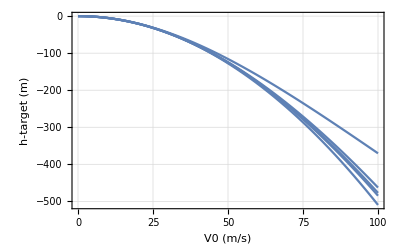

```mathematica
delh=Log[√(1+(v0^2 β)/g)]/β/.β-> (1/2)(rho0)*Cd*A/mdry
subs={rho0-> 0.9, Cd-> 0.5, A->π*(3*0.0254)^2, mdry-> {5, 20, 30, 40}, g-> 9.81}
g1=Plot[{-delh,-v0^2/(2 g)} /.subs,{v0,0,100}, GridLines->Automatic,Frame->True,FrameLabel-> {"V0 (m/s)", "h-target (m)"}]
```

```mathematica
subs={rho0-> 0.9, Cd-> 0.5, A->π*(3*0.0254)^2, mdry->20, g-> 9.81};
h0=400
h0==delh/.subs
```

400

400==4872.9 Log[√(1+0.0000209191 v0^2)]

```mathematica
Solve[400==4872.9018305925565 Log[√(1+0.00002091911610952972 v0^2)]&&v0>0,{v0},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v0→92.3524}}

```mathematica
dv=92.35240033401652- 60
```

32.3524

```mathematica
20*(Exp[dv/2000]-1)
```

0.326155

```mathematica
ScientificForm[(1/2)(rho0)*Cd*A/mdry/.subs]
```

2.05217×10^-4

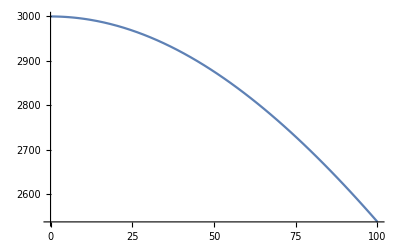

```mathematica
Plot[3000-delh/.subs,{v0,0,100}]
```

```mathematica
Limit[Log[√(1+(v0^2 β)/g)]/β,β-> 0]
```

v0^2/(2 g)

```mathematica
Solve[dh== -delh,v0]
```

{{v0→-(√2 √(-g mdry+ⅇ^(-(A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)},{v0→(√2 √(-g mdry+ⅇ^(-(A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)}}

```mathematica
(*for some h0, v0 = (√2 √(-g mdry+ⅇ^((-A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)*)
```

```mathematica
v0needed=(√2 √(-g mdry+ⅇ^((-A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)
```

(√2 √(-g mdry+ⅇ^(-(A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)

```mathematica
mp =Max[ (Exp[(v0needed-v0)/c]-1),-0.010]
```

Max[-0.01,-1+ⅇ^(((√2 √(-g mdry+ⅇ^(-(A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)-v0)/c)]

```mathematica
mp
```

Max[-0.01,-1+ⅇ^(((√2 √(-g mdry+ⅇ^(-(A Cd dh rho0)/mdry) g mdry))/(√A √Cd √rho0)-v0)/c)]

```mathematica
mp/.subs
```

Max[-0.01,-1+ⅇ^((15.6091 √(-196.2+196.2 ⅇ^(-0.000410433 dh))-v0)/c)]

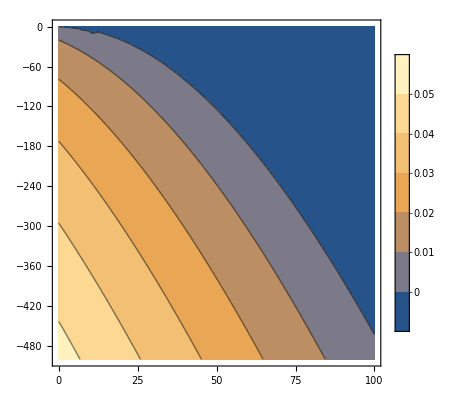

```mathematica
g2=ContourPlot[mp/.subs/.c-> 2000,{v0,0,100},{dh,-500,0},PlotLegends->Automatic]
```

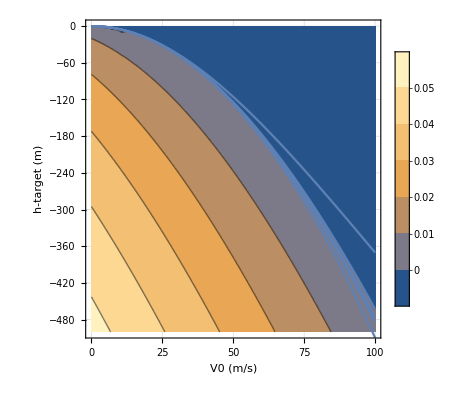

```mathematica
Show[{g2, g1},GridLines->Automatic,Frame->True,FrameLabel-> {"V0 (m/s)", "h-target (m)"}]
```